### Calculate coefficient of determination function

```mathematica
CoefficientRR[ y_, f_]:= 1 - (#.#&[y - f ])/(#.#&[y - Mean[y]])(*Формула для вычисления коэффициента детерминации*)
```

## Data import and formatting

```mathematica
SetDirectory[NotebookDirectory[]];
rawData = Import["summary_SDB (1).xlsx"];
rawData =rawData⟦1⟧
```

{{,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,},{,,,Medium with 5% FBS,,,,,,,,,,,,,,,Serum-free medium,,,,,,,,,,,,,},{,,,Luminescence (RLU),,,,,,,Fluorescence (RFU),,,,,,,,Luminescence (RLU),,,,,,,Fluorescence (RFU),,,,,,},{Tme point,Date,Time (h),50 µg/ml,10 µg/ml,1 µg/ml,0.1 µg/ml,0.01 µg/ml,0 µg/ml,PC,50 µg/ml,10 µg/ml,1 µg/ml,0.1 µg/ml,0.01 µg/ml,0 µg/ml,PC,,50 µg/ml,10 µg/ml,1 µg/ml,0.1 µg/ml,0.01 µg/ml,0 µg/ml,PC,50 µg/ml,10 µg/ml,1 µg/ml,0.1 µg/ml,0.01 µg/ml,0 µg/ml,PC},{T0,20.07.2022 21:35:59,0.,1.17887×10^6,1.1992×10^6,1.46962×10^6,1.44045×10^6,1.40745×10^6,1.21322×10^6,4299.,30.3983,44.9908,30.2558,32.5633,31.4208,28.5118,0.807667,,908694.,1.17092×10^6,1.16969×10^6,1.09737×10^6,1.08577×10^6,881344.,4797.33,7.44808,8.83483,11.2198,12.4548,15.4123,24.5023,57.594},{T1,21.07.2022 00:34:55,3.,2.3114×10^6,2.3044×10^6,3.05715×10^6,2.9089×10^6,2.8469×10^6,2.4469×10^6,2670.33,37.014,53.0465,39.599,47.154,42.819,35.8743,1.08567,,771995.,2.41034×10^6,2.28359×10^6,2.19109×10^6,2.10184×10^6,1.58434×10^6,853.667,16.7827,13.0865,14.405,24.3165,28.464,41.7465,70.639},{T2,21.07.2022 09:57:58,12.5,2.93206×10^6,2.68181×10^6,3.79406×10^6,3.73956×10^6,3.84281×10^6,3.42456×10^6,0.,45.9522,66.1472,45.8047,50.9122,30.0397,23.7779,3.007,,232397.,1.67332×10^6,1.0539×10^6,967897.,957522.,806047.,55.4,43.2007,22.3737,19.7857,27.2857,24.1882,24.9257,85.2007},{T3,21.07.2022 12:56:33,15.5,2.84842×10^6,2.67469×10^6,3.60092×10^6,3.70417×10^6,3.93842×10^6,3.44377×10^6,0.,44.0888,65.2188,45.6438,53.2038,38.6013,29.4951,2.34333,,120550.,1.3036×10^6,860030.,776655.,842805.,717230.,0.,43.7907,22.8857,21.3032,28.6182,29.1707,32.6557,87.0807},{T4,21.07.2022 15:53:44,18.5,3.18434×10^6,2.98322×10^6,3.89959×10^6,4.17634×10^6,4.53809×10^6,4.05559×10^6,0.,40.2593,62.2343,45.4143,54.2593,47.8193,38.2121,1.075,,81039.2,1.05462×10^6,871967.,806692.,893517.,733967.,0.,41.801,27.031,22.0335,33.491,36.166,47.4935,81.6393},{T5,21.07.2022 18:55:34,21.5,2.9683×10^6,2.81913×10^6,3.6533×10^6,3.8593×10^6,4.4423×10^6,3.92903×10^6,0.,39.767,60.592,44.5145,52.6395,49.662,37.6188,1.008,,46720.4,745948.,757093.,711943.,767793.,668768.,0.,41.4375,29.7085,20.8975,32.7125,37.4775,50.55,81.2833},{T6,21.07.2022 21:54:22,24.5,3.25796×10^6,3.10929×10^6,3.90996×10^6,4.18646×10^6,4.90546×10^6,4.10746×10^6,0.,39.4223,59.7398,45.2298,54.3573,49.5548,37.9301,1.04767,,39220.,668983.,765910.,748510.,788060.,680760.,0.,42.2303,32.1883,23.1953,34.6928,38.8103,48.2403,78.2287},{T7,22.07.2022 00:44:51,27.5,3.24315×10^6,3.10823×10^6,3.86515×10^6,4.1689×10^6,4.9534×10^6,4.28653×10^6,0.,39.276,59.3485,46.071,55.606,49.7385,37.6653,0.978,,28122.6,531915.,640313.,710613.,718413.,625738.,0.,43.2462,35.1487,27.3087,36.2762,39.6337,47.8487,82.6203},{T8,22.07.2022 17:11:06,44.,2.98127×10^6,2.95581×10^6,3.04519×10^6,3.89672×10^6,4.82422×10^6,4.14497×10^6,0.,35.7735,54.966,49.8835,57.526,47.126,36.7523,0.940667,,7739.7,145377.,210494.,366297.,397847.,345172.,0.,41.488,49.238,42.2605,44.263,39.388,48.6355,67.1447},{T9,22.07.2022 20:08:28,47.,3.20472×10^6,3.02563×10^6,3.14014×10^6,3.99563×10^6,4.86963×10^6,4.51938×10^6,0.,33.1602,54.4252,46.8077,55.5402,45.6952,35.8172,0.828333,,5951.58,89010.8,129641.,261801.,322789.,276714.,0.,40.9165,51.259,43.139,46.229,39.9965,48.564,67.2907},{T10,22.07.2022 22:58:02,50.,2.76678×10^6,2.72165×10^6,2.83391×10^6,3.50461×10^6,4.29301×10^6,4.10276×10^6,0.,32.9665,53.774,45.8065,55.9265,45.3765,36.336,0.908667,,5694.29,52343.9,79806.4,202143.,283198.,240773.,0.,40.6153,54.2678,45.3353,48.4903,40.6728,47.6853,67.262},{,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,},{,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,},{,0.284138,0.29669,,,,,,,,,,,,,,,,,,,,,,,,,,,,,},{,0.574736,0.617182,,,,,,,,,,,,,,,,,,,,,,,,,,,,,},{,0.775792,0.76595,,,,,,,,,,,,,,,,,,,,,,,,,,,,,},{,0.795093,0.726958,,,,,,,,,,,,,,,,,,,,,,,,,,,,,},{,0.916157,0.787256,,,,,,,,,,,,,,,,,,,,,,,,,,,,,},{,0.896819,0.737534,,,,,,,,,,,,,,,,,,,,,,,,,,,,,},{,0.990322,0.789349,,,,,,,,,,,,,,,,,,,,,,,,,,,,,},{,1.,0.780302,,,,,,,,,,,,,,,,,,,,,,,,,,,,,},{,0.97392,0.614767,,,,,,,,,,,,,,,,,,,,,,,,,,,,,},{,0.983087,0.633935,,,,,,,,,,,,,,,,,,,,,,,,,,,,,},{,0.866678,0.572114,,,,,,,,,,,,,,,,,,,,,,,,,,,,,}}

```mathematica
rawData//MatrixForm
```

( |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  | Medium with 5% FBS |  |  |  |  |  |  |  |  |  |  |  |  |  |  | Serum-free medium |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  | Luminescence (RLU) |  |  |  |  |  |  | Fluorescence (RFU) |  |  |  |  |  |  |  | Luminescence (RLU) |  |  |  |  |  |  | Fluorescence (RFU) |  |  |  |  |  | 
Tme point | Date | Time (h) | 50 µg/ml | 10 µg/ml | 1 µg/ml | 0.1 µg/ml | 0.01 µg/ml | 0 µg/ml | PC | 50 µg/ml | 10 µg/ml | 1 µg/ml | 0.1 µg/ml | 0.01 µg/ml | 0 µg/ml | PC |  | 50 µg/ml | 10 µg/ml | 1 µg/ml | 0.1 µg/ml | 0.01 µg/ml | 0 µg/ml | PC | 50 µg/ml | 10 µg/ml | 1 µg/ml | 0.1 µg/ml | 0.01 µg/ml | 0 µg/ml | PC
T0 | 20.07.2022 21:35:59 | 0. | 1.17887×10^6 | 1.1992×10^6 | 1.46962×10^6 | 1.44045×10^6 | 1.40745×10^6 | 1.21322×10^6 | 4299. | 30.3983 | 44.9908 | 30.2558 | 32.5633 | 31.4208 | 28.5118 | 0.807667 |  | 908694. | 1.17092×10^6 | 1.16969×10^6 | 1.09737×10^6 | 1.08577×10^6 | 881344. | 4797.33 | 7.44808 | 8.83483 | 11.2198 | 12.4548 | 15.4123 | 24.5023 | 57.594
T1 | 21.07.2022 00:34:55 | 3. | 2.3114×10^6 | 2.3044×10^6 | 3.05715×10^6 | 2.9089×10^6 | 2.8469×10^6 | 2.4469×10^6 | 2670.33 | 37.014 | 53.0465 | 39.599 | 47.154 | 42.819 | 35.8743 | 1.08567 |  | 771995. | 2.41034×10^6 | 2.28359×10^6 | 2.19109×10^6 | 2.10184×10^6 | 1.58434×10^6 | 853.667 | 16.7827 | 13.0865 | 14.405 | 24.3165 | 28.464 | 41.7465 | 70.639
T2 | 21.07.2022 09:57:58 | 12.5 | 2.93206×10^6 | 2.68181×10^6 | 3.79406×10^6 | 3.73956×10^6 | 3.84281×10^6 | 3.42456×10^6 | 0. | 45.9522 | 66.1472 | 45.8047 | 50.9122 | 30.0397 | 23.7779 | 3.007 |  | 232397. | 1.67332×10^6 | 1.0539×10^6 | 967897. | 957522. | 806047. | 55.4 | 43.2007 | 22.3737 | 19.7857 | 27.2857 | 24.1882 | 24.9257 | 85.2007
T3 | 21.07.2022 12:56:33 | 15.5 | 2.84842×10^6 | 2.67469×10^6 | 3.60092×10^6 | 3.70417×10^6 | 3.93842×10^6 | 3.44377×10^6 | 0. | 44.0888 | 65.2188 | 45.6438 | 53.2038 | 38.6013 | 29.4951 | 2.34333 |  | 120550. | 1.3036×10^6 | 860030. | 776655. | 842805. | 717230. | 0. | 43.7907 | 22.8857 | 21.3032 | 28.6182 | 29.1707 | 32.6557 | 87.0807
T4 | 21.07.2022 15:53:44 | 18.5 | 3.18434×10^6 | 2.98322×10^6 | 3.89959×10^6 | 4.17634×10^6 | 4.53809×10^6 | 4.05559×10^6 | 0. | 40.2593 | 62.2343 | 45.4143 | 54.2593 | 47.8193 | 38.2121 | 1.075 |  | 81039.2 | 1.05462×10^6 | 871967. | 806692. | 893517. | 733967. | 0. | 41.801 | 27.031 | 22.0335 | 33.491 | 36.166 | 47.4935 | 81.6393
T5 | 21.07.2022 18:55:34 | 21.5 | 2.9683×10^6 | 2.81913×10^6 | 3.6533×10^6 | 3.8593×10^6 | 4.4423×10^6 | 3.92903×10^6 | 0. | 39.767 | 60.592 | 44.5145 | 52.6395 | 49.662 | 37.6188 | 1.008 |  | 46720.4 | 745948. | 757093. | 711943. | 767793. | 668768. | 0. | 41.4375 | 29.7085 | 20.8975 | 32.7125 | 37.4775 | 50.55 | 81.2833
T6 | 21.07.2022 21:54:22 | 24.5 | 3.25796×10^6 | 3.10929×10^6 | 3.90996×10^6 | 4.18646×10^6 | 4.90546×10^6 | 4.10746×10^6 | 0. | 39.4223 | 59.7398 | 45.2298 | 54.3573 | 49.5548 | 37.9301 | 1.04767 |  | 39220. | 668983. | 765910. | 748510. | 788060. | 680760. | 0. | 42.2303 | 32.1883 | 23.1953 | 34.6928 | 38.8103 | 48.2403 | 78.2287
T7 | 22.07.2022 00:44:51 | 27.5 | 3.24315×10^6 | 3.10823×10^6 | 3.86515×10^6 | 4.1689×10^6 | 4.9534×10^6 | 4.28653×10^6 | 0. | 39.276 | 59.3485 | 46.071 | 55.606 | 49.7385 | 37.6653 | 0.978 |  | 28122.6 | 531915. | 640313. | 710613. | 718413. | 625738. | 0. | 43.2462 | 35.1487 | 27.3087 | 36.2762 | 39.6337 | 47.8487 | 82.6203
T8 | 22.07.2022 17:11:06 | 44. | 2.98127×10^6 | 2.95581×10^6 | 3.04519×10^6 | 3.89672×10^6 | 4.82422×10^6 | 4.14497×10^6 | 0. | 35.7735 | 54.966 | 49.8835 | 57.526 | 47.126 | 36.7523 | 0.940667 |  | 7739.7 | 145377. | 210494. | 366297. | 397847. | 345172. | 0. | 41.488 | 49.238 | 42.2605 | 44.263 | 39.388 | 48.6355 | 67.1447
T9 | 22.07.2022 20:08:28 | 47. | 3.20472×10^6 | 3.02563×10^6 | 3.14014×10^6 | 3.99563×10^6 | 4.86963×10^6 | 4.51938×10^6 | 0. | 33.1602 | 54.4252 | 46.8077 | 55.5402 | 45.6952 | 35.8172 | 0.828333 |  | 5951.58 | 89010.8 | 129641. | 261801. | 322789. | 276714. | 0. | 40.9165 | 51.259 | 43.139 | 46.229 | 39.9965 | 48.564 | 67.2907
T10 | 22.07.2022 22:58:02 | 50. | 2.76678×10^6 | 2.72165×10^6 | 2.83391×10^6 | 3.50461×10^6 | 4.29301×10^6 | 4.10276×10^6 | 0. | 32.9665 | 53.774 | 45.8065 | 55.9265 | 45.3765 | 36.336 | 0.908667 |  | 5694.29 | 52343.9 | 79806.4 | 202143. | 283198. | 240773. | 0. | 40.6153 | 54.2678 | 45.3353 | 48.4903 | 40.6728 | 47.6853 | 67.262
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0.284138 | 0.29669 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0.574736 | 0.617182 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0.775792 | 0.76595 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0.795093 | 0.726958 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0.916157 | 0.787256 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0.896819 | 0.737534 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0.990322 | 0.789349 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 1. | 0.780302 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0.97392 | 0.614767 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0.983087 | 0.633935 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0.866678 | 0.572114 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | )

```mathematica
data = rawData⟦4;;15⟧
```

{{Tme point,Date,Time (h),50 µg/ml,10 µg/ml,1 µg/ml,0.1 µg/ml,0.01 µg/ml,0 µg/ml,PC,50 µg/ml,10 µg/ml,1 µg/ml,0.1 µg/ml,0.01 µg/ml,0 µg/ml,PC,,50 µg/ml,10 µg/ml,1 µg/ml,0.1 µg/ml,0.01 µg/ml,0 µg/ml,PC,50 µg/ml,10 µg/ml,1 µg/ml,0.1 µg/ml,0.01 µg/ml,0 µg/ml,PC},{T0,20.07.2022 21:35:59,0.,1.17887×10^6,1.1992×10^6,1.46962×10^6,1.44045×10^6,1.40745×10^6,1.21322×10^6,4299.,30.3983,44.9908,30.2558,32.5633,31.4208,28.5118,0.807667,,908694.,1.17092×10^6,1.16969×10^6,1.09737×10^6,1.08577×10^6,881344.,4797.33,7.44808,8.83483,11.2198,12.4548,15.4123,24.5023,57.594},{T1,21.07.2022 00:34:55,3.,2.3114×10^6,2.3044×10^6,3.05715×10^6,2.9089×10^6,2.8469×10^6,2.4469×10^6,2670.33,37.014,53.0465,39.599,47.154,42.819,35.8743,1.08567,,771995.,2.41034×10^6,2.28359×10^6,2.19109×10^6,2.10184×10^6,1.58434×10^6,853.667,16.7827,13.0865,14.405,24.3165,28.464,41.7465,70.639},{T2,21.07.2022 09:57:58,12.5,2.93206×10^6,2.68181×10^6,3.79406×10^6,3.73956×10^6,3.84281×10^6,3.42456×10^6,0.,45.9522,66.1472,45.8047,50.9122,30.0397,23.7779,3.007,,232397.,1.67332×10^6,1.0539×10^6,967897.,957522.,806047.,55.4,43.2007,22.3737,19.7857,27.2857,24.1882,24.9257,85.2007},{T3,21.07.2022 12:56:33,15.5,2.84842×10^6,2.67469×10^6,3.60092×10^6,3.70417×10^6,3.93842×10^6,3.44377×10^6,0.,44.0888,65.2188,45.6438,53.2038,38.6013,29.4951,2.34333,,120550.,1.3036×10^6,860030.,776655.,842805.,717230.,0.,43.7907,22.8857,21.3032,28.6182,29.1707,32.6557,87.0807},{T4,21.07.2022 15:53:44,18.5,3.18434×10^6,2.98322×10^6,3.89959×10^6,4.17634×10^6,4.53809×10^6,4.05559×10^6,0.,40.2593,62.2343,45.4143,54.2593,47.8193,38.2121,1.075,,81039.2,1.05462×10^6,871967.,806692.,893517.,733967.,0.,41.801,27.031,22.0335,33.491,36.166,47.4935,81.6393},{T5,21.07.2022 18:55:34,21.5,2.9683×10^6,2.81913×10^6,3.6533×10^6,3.8593×10^6,4.4423×10^6,3.92903×10^6,0.,39.767,60.592,44.5145,52.6395,49.662,37.6188,1.008,,46720.4,745948.,757093.,711943.,767793.,668768.,0.,41.4375,29.7085,20.8975,32.7125,37.4775,50.55,81.2833},{T6,21.07.2022 21:54:22,24.5,3.25796×10^6,3.10929×10^6,3.90996×10^6,4.18646×10^6,4.90546×10^6,4.10746×10^6,0.,39.4223,59.7398,45.2298,54.3573,49.5548,37.9301,1.04767,,39220.,668983.,765910.,748510.,788060.,680760.,0.,42.2303,32.1883,23.1953,34.6928,38.8103,48.2403,78.2287},{T7,22.07.2022 00:44:51,27.5,3.24315×10^6,3.10823×10^6,3.86515×10^6,4.1689×10^6,4.9534×10^6,4.28653×10^6,0.,39.276,59.3485,46.071,55.606,49.7385,37.6653,0.978,,28122.6,531915.,640313.,710613.,718413.,625738.,0.,43.2462,35.1487,27.3087,36.2762,39.6337,47.8487,82.6203},{T8,22.07.2022 17:11:06,44.,2.98127×10^6,2.95581×10^6,3.04519×10^6,3.89672×10^6,4.82422×10^6,4.14497×10^6,0.,35.7735,54.966,49.8835,57.526,47.126,36.7523,0.940667,,7739.7,145377.,210494.,366297.,397847.,345172.,0.,41.488,49.238,42.2605,44.263,39.388,48.6355,67.1447},{T9,22.07.2022 20:08:28,47.,3.20472×10^6,3.02563×10^6,3.14014×10^6,3.99563×10^6,4.86963×10^6,4.51938×10^6,0.,33.1602,54.4252,46.8077,55.5402,45.6952,35.8172,0.828333,,5951.58,89010.8,129641.,261801.,322789.,276714.,0.,40.9165,51.259,43.139,46.229,39.9965,48.564,67.2907},{T10,22.07.2022 22:58:02,50.,2.76678×10^6,2.72165×10^6,2.83391×10^6,3.50461×10^6,4.29301×10^6,4.10276×10^6,0.,32.9665,53.774,45.8065,55.9265,45.3765,36.336,0.908667,,5694.29,52343.9,79806.4,202143.,283198.,240773.,0.,40.6153,54.2678,45.3353,48.4903,40.6728,47.6853,67.262}}

```mathematica
dataᵀ
```

{{Tme point,T0,T1,T2,T3,T4,T5,T6,T7,T8,T9,T10},{Date,20.07.2022 21:35:59,21.07.2022 00:34:55,21.07.2022 09:57:58,21.07.2022 12:56:33,21.07.2022 15:53:44,21.07.2022 18:55:34,21.07.2022 21:54:22,22.07.2022 00:44:51,22.07.2022 17:11:06,22.07.2022 20:08:28,22.07.2022 22:58:02},{Time (h),0.,3.,12.5,15.5,18.5,21.5,24.5,27.5,44.,47.,50.},{50 µg/ml,1.17887×10^6,2.3114×10^6,2.93206×10^6,2.84842×10^6,3.18434×10^6,2.9683×10^6,3.25796×10^6,3.24315×10^6,2.98127×10^6,3.20472×10^6,2.76678×10^6},{10 µg/ml,1.1992×10^6,2.3044×10^6,2.68181×10^6,2.67469×10^6,2.98322×10^6,2.81913×10^6,3.10929×10^6,3.10823×10^6,2.95581×10^6,3.02563×10^6,2.72165×10^6},{1 µg/ml,1.46962×10^6,3.05715×10^6,3.79406×10^6,3.60092×10^6,3.89959×10^6,3.6533×10^6,3.90996×10^6,3.86515×10^6,3.04519×10^6,3.14014×10^6,2.83391×10^6},{0.1 µg/ml,1.44045×10^6,2.9089×10^6,3.73956×10^6,3.70417×10^6,4.17634×10^6,3.8593×10^6,4.18646×10^6,4.1689×10^6,3.89672×10^6,3.99563×10^6,3.50461×10^6},{0.01 µg/ml,1.40745×10^6,2.8469×10^6,3.84281×10^6,3.93842×10^6,4.53809×10^6,4.4423×10^6,4.90546×10^6,4.9534×10^6,4.82422×10^6,4.86963×10^6,4.29301×10^6},{0 µg/ml,1.21322×10^6,2.4469×10^6,3.42456×10^6,3.44377×10^6,4.05559×10^6,3.92903×10^6,4.10746×10^6,4.28653×10^6,4.14497×10^6,4.51938×10^6,4.10276×10^6},{PC,4299.,2670.33,0.,0.,0.,0.,0.,0.,0.,0.,0.},{50 µg/ml,30.3983,37.014,45.9522,44.0888,40.2593,39.767,39.4223,39.276,35.7735,33.1602,32.9665},{10 µg/ml,44.9908,53.0465,66.1472,65.2188,62.2343,60.592,59.7398,59.3485,54.966,54.4252,53.774},{1 µg/ml,30.2558,39.599,45.8047,45.6438,45.4143,44.5145,45.2298,46.071,49.8835,46.8077,45.8065},{0.1 µg/ml,32.5633,47.154,50.9122,53.2038,54.2593,52.6395,54.3573,55.606,57.526,55.5402,55.9265},{0.01 µg/ml,31.4208,42.819,30.0397,38.6013,47.8193,49.662,49.5548,49.7385,47.126,45.6952,45.3765},{0 µg/ml,28.5118,35.8743,23.7779,29.4951,38.2121,37.6188,37.9301,37.6653,36.7523,35.8172,36.336},{PC,0.807667,1.08567,3.007,2.34333,1.075,1.008,1.04767,0.978,0.940667,0.828333,0.908667},{,,,,,,,,,,,},{50 µg/ml,908694.,771995.,232397.,120550.,81039.2,46720.4,39220.,28122.6,7739.7,5951.58,5694.29},{10 µg/ml,1.17092×10^6,2.41034×10^6,1.67332×10^6,1.3036×10^6,1.05462×10^6,745948.,668983.,531915.,145377.,89010.8,52343.9},{1 µg/ml,1.16969×10^6,2.28359×10^6,1.0539×10^6,860030.,871967.,757093.,765910.,640313.,210494.,129641.,79806.4},{0.1 µg/ml,1.09737×10^6,2.19109×10^6,967897.,776655.,806692.,711943.,748510.,710613.,366297.,261801.,202143.},{0.01 µg/ml,1.08577×10^6,2.10184×10^6,957522.,842805.,893517.,767793.,788060.,718413.,397847.,322789.,283198.},{0 µg/ml,881344.,1.58434×10^6,806047.,717230.,733967.,668768.,680760.,625738.,345172.,276714.,240773.},{PC,4797.33,853.667,55.4,0.,0.,0.,0.,0.,0.,0.,0.},{50 µg/ml,7.44808,16.7827,43.2007,43.7907,41.801,41.4375,42.2303,43.2462,41.488,40.9165,40.6153},{10 µg/ml,8.83483,13.0865,22.3737,22.8857,27.031,29.7085,32.1883,35.1487,49.238,51.259,54.2678},{1 µg/ml,11.2198,14.405,19.7857,21.3032,22.0335,20.8975,23.1953,27.3087,42.2605,43.139,45.3353},{0.1 µg/ml,12.4548,24.3165,27.2857,28.6182,33.491,32.7125,34.6928,36.2762,44.263,46.229,48.4903},{0.01 µg/ml,15.4123,28.464,24.1882,29.1707,36.166,37.4775,38.8103,39.6337,39.388,39.9965,40.6728},{0 µg/ml,24.5023,41.7465,24.9257,32.6557,47.4935,50.55,48.2403,47.8487,48.6355,48.564,47.6853},{PC,57.594,70.639,85.2007,87.0807,81.6393,81.2833,78.2287,82.6203,67.1447,67.2907,67.262}}

```mathematica
ToExpression@First@StringCases[dataᵀ⟦4,1⟧,NumberString]
```

50

```mathematica
dataᵀ⟦3⟧
```

{Time (h),0.,3.,12.5,15.5,18.5,21.5,24.5,27.5,44.,47.,50.}

```mathematica
Rest@dataᵀ⟦4⟧/231000
```

{5.10335,10.0061,12.6929,12.3308,13.785,12.8498,14.1037,14.0396,12.9059,13.8732,11.9774}

```mathematica
Rest@dataᵀ⟦3⟧
```

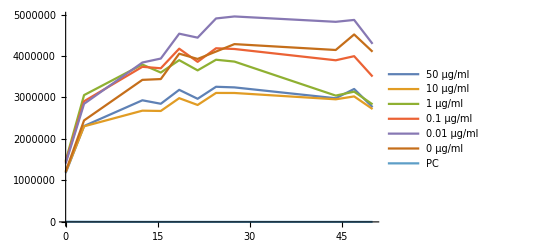

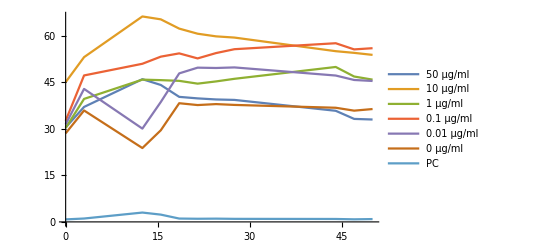

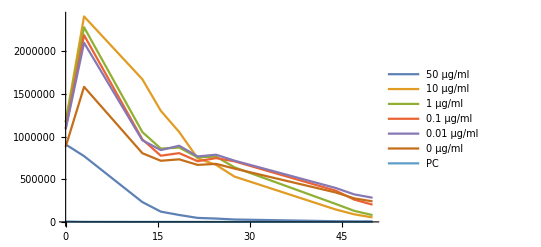

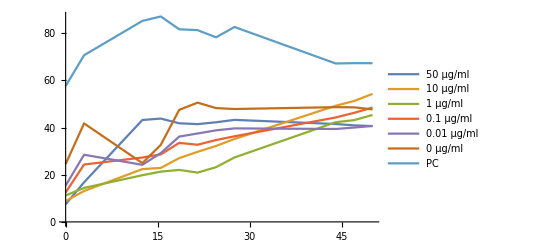

```mathematica
Table[Table[{Rest@dataᵀ⟦3⟧,Rest@dataᵀ⟦i⟧}ᵀ,{i,j,j+6}],{j,{4,11,19,26}}];
Print@ListLinePlot[#,PlotLegends->data⟦1,4;;10⟧]&/@% ;
```

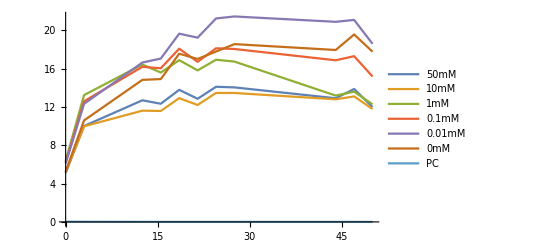

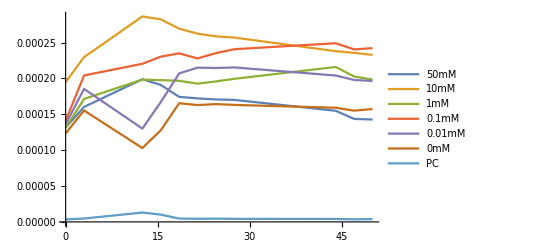

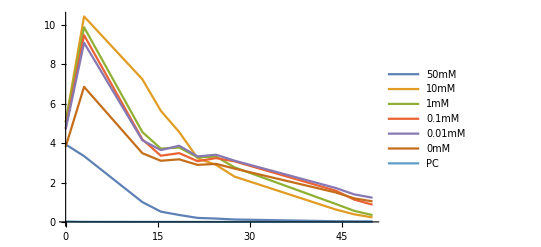

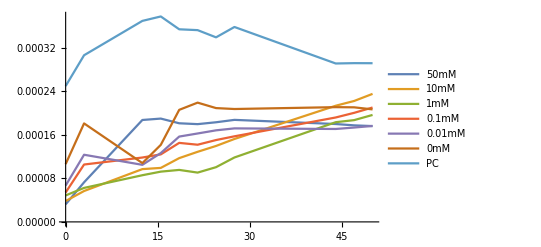

```mathematica
Table[Table[{Rest@dataᵀ⟦3⟧,Rest@dataᵀ⟦i⟧/231000}ᵀ,{i,j,j+6}],{j,{4,11,19,26}}];
If[StringContainsQ[#, NumberString],StringForm["``mM",First@StringCases[#, NumberString]], "PC"]&/@ data⟦1,4;;10⟧;
Print@ListLinePlot[#,PlotLegends->%]&/@%% ;
```

```mathematica
train0 = Table[Table[{Rest@dataᵀ⟦3⟧,ConstantArray[ToExpression@First@StringCases[dataᵀ⟦i,1⟧,NumberString] ,11],Rest@dataᵀ⟦i⟧/231000}ᵀ,{i,j,j+5}],{j,{4,11,19,26}}];
```

```mathematica
Print@ListPointPlot3D[#]&/@ train0;
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

```mathematica
Dimensions[train0]
```

{4,6,11,3}

```mathematica
max = Max[train0⟦All,All, All, 3⟧]
```

21.4433

```mathematica
train1 = ArrayReshape[#/{1,1,max}&/@Flatten[train0,2], {4,66, 3}];
```

```mathematica
firsts = train0⟦All,All,1, 3⟧
```

{{5.10335,5.19134,6.36201,6.23571,6.09285,5.25205},{0.000131595,0.000194766,0.000130978,0.000140967,0.000136021,0.000123428},{3.93374,5.06891,5.06361,4.75052,4.7003,3.81534},{0.0000322428,0.000038246,0.0000485707,0.000053917,0.0000667201,0.000106071}}

```mathematica
train1//Dimensions
```

{4,66,3}

```mathematica
train2 = ArrayReshape[Table[#/{1, 1, firsts⟦i,j⟧}&/@train0⟦i, j⟧,{i,1, 4},{j, 1, 6}], {4, 66,3}]
```

{{{0.,50,1.},{3.,50,1.96068},{12.5,50,2.48717},{15.5,50,2.41622},{18.5,50,2.70117},{21.5,50,2.51791},{24.5,50,2.76362},{27.5,50,2.75106},{44.,50,2.52891},{47.,50,2.71845},{50.,50,2.34697},{0.,10,1.},{3.,10,1.92162},{12.5,10,2.23633},{15.5,10,2.2304},{18.5,10,2.48768},{21.5,10,2.35084},{24.5,10,2.5928},{27.5,10,2.59192},{44.,10,2.46482},{47.,10,2.52304},{50.,10,2.26956},{0.,1,1.},{3.,1,2.08023},{12.5,1,2.58165},{15.5,1,2.45023},{18.5,1,2.65346},{21.5,1,2.48587},{24.5,1,2.66052},{27.5,1,2.63003},{44.,1,2.07209},{47.,1,2.13669},{50.,1,1.92832},{0.,0.1,1.},{3.,0.1,2.01944},{12.5,0.1,2.59611},{15.5,0.1,2.57154},{18.5,0.1,2.89933},{21.5,0.1,2.67924},{24.5,0.1,2.90636},{27.5,0.1,2.89417},{44.,0.1,2.70521},{47.,0.1,2.77387},{50.,0.1,2.43299},{0.,0.01,1.},{3.,0.01,2.02274},{12.5,0.01,2.73034},{15.5,0.01,2.79827},{18.5,0.01,3.22434},{21.5,0.01,3.15628},{24.5,0.01,3.48536},{27.5,0.01,3.51942},{44.,0.01,3.42763},{47.,0.01,3.45989},{50.,0.01,3.0502},{0.,0,1.},{3.,0,2.01686},{12.5,0,2.82269},{15.5,0,2.83852},{18.5,0,3.34282},{21.5,0,3.2385},{24.5,0,3.38558},{27.5,0,3.53317},{44.,0,3.41649},{47.,0,3.7251},{50.,0,3.3817}},{{0.,50,1.},{3.,50,1.21763},{12.5,50,1.51167},{15.5,50,1.45037},{18.5,50,1.32439},{21.5,50,1.3082},{24.5,50,1.29686},{27.5,50,1.29204},{44.,50,1.17682},{47.,50,1.09085},{50.,50,1.08448},{0.,10,1.},{3.,10,1.17905},{12.5,10,1.47024},{15.5,10,1.4496},{18.5,10,1.38327},{21.5,10,1.34676},{24.5,10,1.32782},{27.5,10,1.31912},{44.,10,1.22172},{47.,10,1.20969},{50.,10,1.19522},{0.,1,1.},{3.,1,1.30881},{12.5,1,1.51391},{15.5,1,1.5086},{18.5,1,1.50101},{21.5,1,1.47127},{24.5,1,1.49491},{27.5,1,1.52271},{44.,1,1.64872},{47.,1,1.54706},{50.,1,1.51397},{0.,0.1,1.},{3.,0.1,1.44807},{12.5,0.1,1.56348},{15.5,0.1,1.63386},{18.5,0.1,1.66627},{21.5,0.1,1.61653},{24.5,0.1,1.66928},{27.5,0.1,1.70763},{44.,0.1,1.76659},{47.,0.1,1.7056},{50.,0.1,1.71747},{0.,0.01,1.},{3.,0.01,1.36276},{12.5,0.01,0.956043},{15.5,0.01,1.22853},{18.5,0.01,1.5219},{21.5,0.01,1.58054},{24.5,0.01,1.57713},{27.5,0.01,1.58298},{44.,0.01,1.49983},{47.,0.01,1.4543},{50.,0.01,1.44415},{0.,0,1.},{3.,0,1.25822},{12.5,0,0.833967},{15.5,0,1.03449},{18.5,0,1.34022},{21.5,0,1.31941},{24.5,0,1.33033},{27.5,0,1.32104},{44.,0,1.28902},{47.,0,1.25622},{50.,0,1.27442}},{{0.,50,1.},{3.,50,0.849565},{12.5,50,0.255748},{15.5,50,0.132663},{18.5,50,0.0891821},{21.5,50,0.0514149},{24.5,50,0.0431609},{27.5,50,0.0309483},{44.,50,0.00851739},{47.,50,0.0065496},{50.,50,0.00626646},{0.,10,1.},{3.,10,2.05851},{12.5,10,1.42907},{15.5,10,1.11332},{18.5,10,0.900674},{21.5,10,0.637062},{24.5,10,0.571331},{27.5,10,0.454271},{44.,10,0.124157},{47.,10,0.0760179},{50.,10,0.0447033},{0.,1,1.},{3.,1,1.9523},{12.5,1,0.901002},{15.5,1,0.73526},{18.5,1,0.745466},{21.5,1,0.647257},{24.5,1,0.654795},{27.5,1,0.547419},{44.,1,0.179957},{47.,1,0.110833},{50.,1,0.0682285},{0.,0.1,1.},{3.,0.1,1.99668},{12.5,0.1,0.882016},{15.5,0.1,0.707743},{18.5,0.1,0.735114},{21.5,0.1,0.648773},{24.5,0.1,0.682095},{27.5,0.1,0.64756},{44.,0.1,0.333795},{47.,0.1,0.238572},{50.,0.1,0.184207},{0.,0.01,1.},{3.,0.01,1.93581},{12.5,0.01,0.881884},{15.5,0.01,0.776228},{18.5,0.01,0.822934},{21.5,0.01,0.707142},{24.5,0.01,0.725808},{27.5,0.01,0.661662},{44.,0.01,0.366419},{47.,0.01,0.297291},{50.,0.01,0.260827},{0.,0,1.},{3.,0,1.79765},{12.5,0,0.914565},{15.5,0,0.813791},{18.5,0,0.832781},{21.5,0,0.758805},{24.5,0,0.772411},{27.5,0,0.709981},{44.,0,0.391642},{47.,0,0.313968},{50.,0,0.273188}},{{0.,50,1.},{3.,50,2.2533},{12.5,50,5.80024},{15.5,50,5.87945},{18.5,50,5.61232},{21.5,50,5.56351},{24.5,50,5.66996},{27.5,50,5.80635},{44.,50,5.57029},{47.,50,5.49356},{50.,50,5.45313},{0.,10,1.},{3.,10,1.48124},{12.5,10,2.53244},{15.5,10,2.59039},{18.5,10,3.05959},{21.5,10,3.36266},{24.5,10,3.64334},{27.5,10,3.97842},{44.,10,5.57317},{47.,10,5.80192},{50.,10,6.14249},{0.,1,1.},{3.,1,1.28389},{12.5,1,1.76345},{15.5,1,1.89871},{18.5,1,1.9638},{21.5,1,1.86255},{24.5,1,2.06735},{27.5,1,2.43396},{44.,1,3.76659},{47.,1,3.84489},{50.,1,4.04064},{0.,0.1,1.},{3.,0.1,1.95237},{12.5,0.1,2.19077},{15.5,0.1,2.29776},{18.5,0.1,2.689},{21.5,0.1,2.62649},{24.5,0.1,2.78549},{27.5,0.1,2.91262},{44.,0.1,3.55388},{47.,0.1,3.71173},{50.,0.1,3.89329},{0.,0.01,1.},{3.,0.01,1.84683},{12.5,0.01,1.5694},{15.5,0.01,1.89268},{18.5,0.01,2.34656},{21.5,0.01,2.43166},{24.5,0.01,2.51813},{27.5,0.01,2.57156},{44.,0.01,2.55562},{47.,0.01,2.5951},{50.,0.01,2.63898},{0.,0,1.},{3.,0,1.70378},{12.5,0,1.01728},{15.5,0,1.33276},{18.5,0,1.93833},{21.5,0,2.06307},{24.5,0,1.96881},{27.5,0,1.95282},{44.,0,1.98493},{47.,0,1.98202},{50.,0,1.94615}}}

## δ calculations

```mathematica
train0⟦2, -1,All,{1,3}⟧
```

{{0.,0.000123428},{3.,0.0001553},{12.5,0.000102935},{15.5,0.000127684},{18.5,0.00016542},{21.5,0.000162852},{24.5,0.000164199},{27.5,0.000163053},{44.,0.000159101},{47.,0.000155053},{50.,0.000157299}}

```mathematica
train2⟦1, -9;;⟧
```

{{12.5,0,2.82269},{15.5,0,2.83852},{18.5,0,3.34282},{21.5,0,3.2385},{24.5,0,3.38558},{27.5,0,3.53317},{44.,0,3.41649},{47.,0,3.7251},{50.,0,3.3817}}

```mathematica
train2⟦1, -9;;⟧;
#/{1, 1,train0⟦1,-1,3, 3⟧/firsts⟦1,-1⟧}&/@%;
train3 = %
```

{{12.5,0,1.},{15.5,0,1.00561},{18.5,0,1.18427},{21.5,0,1.14731},{24.5,0,1.19941},{27.5,0,1.2517},{44.,0,1.21037},{47.,0,1.3197},{50.,0,1.19804}}

{δ→-0.00510361}

-0.00510361

ⅇ^(0.00510361 t)

Error:0.21384

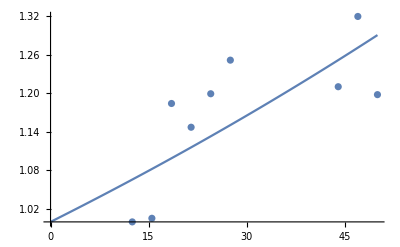

```mathematica
FindFit[train3⟦ All,{1, 3}⟧,ⅇ^(-δ t),{δ}, t]
γ1 = δ/.%
ⅇ^(-δ t)/.%%
%/.t-> train3⟦ All,1⟧;
StringForm["Error:``",√((%- train3⟦All, 3⟧)^2//Total)]
Show[Plot[%%%, {t, 0, 50}], ListPlot[train3⟦All, {1,3}⟧], PlotRange-> All]
```

{δ→-0.0295066}

ⅇ^(0.0295066 t)

{1.44604,1.57988,1.72611,1.88587,2.06042,2.25113,3.66302,4.00206,4.37247}

1.38239

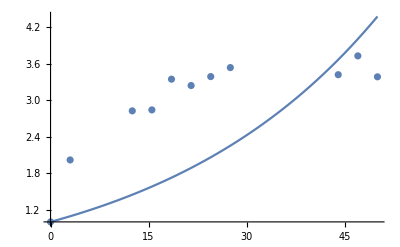

```mathematica
FindFit[train2⟦1, -9;;, {1, 3}⟧,ⅇ^(-δ t),{δ}, t]
ⅇ^(-δ t)/.%
%/.t-> train2⟦1, -9;;, 1⟧
(%- train2⟦1, -9;;, 3⟧)^2//Mean
Show[Plot[%%%, {t, 0, 50}], ListPlot[train2⟦1, -11;;, {1, 3}⟧]]
```

```mathematica
train2⟦3, -10;;⟧
```

{{3.,0,1.79765},{12.5,0,0.914565},{15.5,0,0.813791},{18.5,0,0.832781},{21.5,0,0.758805},{24.5,0,0.772411},{27.5,0,0.709981},{44.,0,0.391642},{47.,0,0.313968},{50.,0,0.273188}}

{δ→0.0393284}

0.0393284

ⅇ^(-0.0393284 t)

Error:0.198006

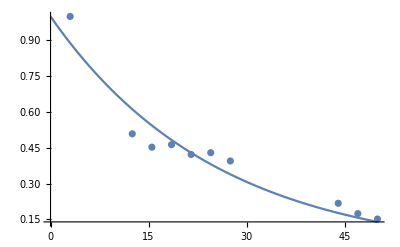

```mathematica
train2⟦3, -10;;⟧;
#/{1, 1,train0⟦3,-1,2, 3⟧/firsts⟦3, -1⟧}&/@%;
train31 = %;
FindFit[train31⟦ All,{1, 3}⟧,ⅇ^(-δ t),{δ}, t]
γ3 = δ/.%
ⅇ^(-δ t)/.%%
%/.t-> train31⟦ All,1⟧;
StringForm["Error:``",√((%- train31⟦All, 3⟧)^2//Total)]
Show[Plot[%%%, {t, 0, 50}], ListPlot[train31⟦All, {1,3}⟧], PlotRange-> All]
```

## Calculations with exponential models (экспоненциальные модели из курсовой работы)

### Model 1

```mathematica
train0⟦1⟧;
x = DeleteCases[%,a_/;a⟦1⟧<10,2];
%⟦;;,1,3⟧;
MapThread[#1⟦;;,3⟧/#2&,{%%,%}];
x⟦;;,;;, 3⟧= %;
X = Flatten[x,1]
```

{{12.5,50,1.},{15.5,50,0.971473},{18.5,50,1.08604},{21.5,50,1.01236},{24.5,50,1.11115},{27.5,50,1.1061},{44.,50,1.01678},{47.,50,1.09299},{50.,50,0.94363},{12.5,10,1.},{15.5,10,0.997346},{18.5,10,1.11239},{21.5,10,1.0512},{24.5,10,1.1594},{27.5,10,1.159},{44.,10,1.10217},{47.,10,1.12821},{50.,10,1.01486},{12.5,1,1.},{15.5,1,0.949093},{18.5,1,1.02782},{21.5,1,0.962901},{24.5,1,1.03055},{27.5,1,1.01874},{44.,1,0.80262},{47.,1,0.827645},{50.,1,0.746933},{12.5,0.1,1.},{15.5,0.1,0.990536},{18.5,0.1,1.1168},{21.5,0.1,1.03202},{24.5,0.1,1.11951},{27.5,0.1,1.11481},{44.,0.1,1.04203},{47.,0.1,1.06848},{50.,0.1,0.937171},{12.5,0.01,1.},{15.5,0.01,1.02488},{18.5,0.01,1.18093},{21.5,0.01,1.156},{24.5,0.01,1.27653},{27.5,0.01,1.28901},{44.,0.01,1.25539},{47.,0.01,1.2672},{50.,0.01,1.11715},{12.5,0,1.},{15.5,0,1.00561},{18.5,0,1.18427},{21.5,0,1.14731},{24.5,0,1.19941},{27.5,0,1.2517},{44.,0,1.21037},{47.,0,1.3197},{50.,0,1.19804}}

```mathematica
X1 = #/{1,231.,1}&/@X⟦;;-10⟧;
```

```mathematica
Rest@dataᵀ⟦3,3;;⟧
```

{12.5,15.5,18.5,21.5,24.5,27.5,44.,47.,50.}

```mathematica
ClearAll[t,x]
```

```mathematica
k = 1;
FindFit[X1,{ Exp[-γ1 x + (t μ)/β^2(1-ⅇ^(-β x)-β x)], μ>0, β>0},{μ ,β},{x,t}, Method->NMinimize]
Exp[- γ1 x + (t μ)/β^2(1-ⅇ^(-β x)-β x)]/. %
Show[ ListPointPlot3D[X1],Plot3D[%,{x,0,50},{t, 0,50/231}, AxesLabel->Automatic], PlotRange-> All]
StringForm["μ/β = ``",( μ/β)/. %%%]
(%%%/.{x-> #⟦1⟧, t-> #⟦2⟧})&/@Flatten[Table[{x,t},{t, {50,10,1,0.1,0.01}/231},{x, Rest@dataᵀ⟦3,3;;⟧}],1];
StringForm["MAE: ``",Mean@Abs[X1⟦;;,3⟧-%]]
StringForm["R:``",CoefficientRR[X1⟦;;,3⟧ , %%]]
```

NMinimize::nnum: The function value Experimental`NumericalFunction[«1»][{0,0}] is not a number at {β,μ} = {0.,0.}.

{μ→0.00150325,β→0.026168}

ⅇ^(2.19528 t (1-ⅇ^(-0.026168 x)-0.026168 x)+0.00510361 x)

-Graphics3D-

μ/β = 0.0574461

MAE: 0.110877

R:-1.07129

```mathematica
k = 2;
FindFit[train⟦k⟧,{ Exp[-0.053x + (t μ)/β^2(1-ⅇ^(-β x)-β x)], μ>0},{μ ,β},{x,t}]
Exp[- 0.053x + (t μ)/β^2(1-ⅇ^(-β x)-β x)]/. %
Show[ ListPointPlot3D[train⟦k⟧],Plot3D[%,{x,0,50},{t, 0,50}, AxesLabel->Automatic]]
StringForm["μ/β = ``",( μ/β)/. %%%]
(%%%/.{x-> #⟦1⟧, t-> #⟦2⟧})&/@Flatten[Table[{x,t},{t, {50,10,1,0.1,0.01,0}},{x, Rest@dataᵀ⟦3⟧}],1];
StringForm["MAE: ``",Mean@Abs[train⟦k,;;,3⟧-%]]
StringForm["R:``",CoefficientRR[train⟦k,;;,3⟧ , %%]]
```

{μ→6.96741×10^-7,β→25389.3}

ⅇ^(1.08086×10^-15 t (1-ⅇ^(-25389.3 x)-25389.3 x)-0.053 x)

-Graphics3D-

μ/β = 2.74423×10^-11

General::munfl: Exp[-76167.9] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-317366.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-393534.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

MAE: 0.974067

R:-22.9575

```mathematica
train0⟦3⟧;
y = DeleteCases[%,a_/;a⟦1⟧<3,2];
%⟦;;,1,3⟧;
MapThread[#1⟦;;,3⟧/#2&,{%%,%}];
y⟦;;,;;, 3⟧= %;
Y = Flatten[y,1]
```

{{3.,50,1.},{12.5,50,0.301034},{15.5,50,0.156154},{18.5,50,0.104974},{21.5,50,0.0605191},{24.5,50,0.0508035},{27.5,50,0.0364284},{44.,50,0.0100256},{47.,50,0.00770936},{50.,50,0.00737608},{3.,10,1.},{12.5,10,0.694225},{15.5,10,0.540837},{18.5,10,0.437538},{21.5,10,0.309478},{24.5,10,0.277546},{27.5,10,0.22068},{44.,10,0.060314},{47.,10,0.0369287},{50.,10,0.0217164},{3.,1,1.},{12.5,1,0.461508},{15.5,1,0.376612},{18.5,1,0.38184},{21.5,1,0.331536},{24.5,1,0.335397},{27.5,1,0.280397},{44.,1,0.0921768},{47.,1,0.0567706},{50.,1,0.0349477},{3.,0.1,1.},{12.5,0.1,0.441741},{15.5,0.1,0.35446},{18.5,0.1,0.368168},{21.5,0.1,0.324926},{24.5,0.1,0.341615},{27.5,0.1,0.324319},{44.,0.1,0.167175},{47.,0.1,0.119484},{50.,0.1,0.0922565},{3.,0.01,1.},{12.5,0.01,0.455563},{15.5,0.01,0.400983},{18.5,0.01,0.425111},{21.5,0.01,0.365295},{24.5,0.01,0.374937},{27.5,0.01,0.341801},{44.,0.01,0.189285},{47.,0.01,0.153574},{50.,0.01,0.134738},{3.,0,1.},{12.5,0,0.508757},{15.5,0,0.452698},{18.5,0,0.463262},{21.5,0,0.42211},{24.5,0,0.429679},{27.5,0,0.39495},{44.,0,0.217864},{47.,0,0.174655},{50.,0,0.15197}}

```mathematica
Y⟦;;-11⟧;
Y1 = #/{1,231.,1}&/@%;
```

```mathematica
k = 3;
FindFit[Y1,{ Exp[-γ3 x + (t μ)/β^2(1-ⅇ^(-β x)-β x)], μ>0, β>0},{μ ,β},{x,t}, Method->NMinimize]
Exp[- γ3 x + (t μ)/β^2(1-ⅇ^(-β x)-β x)]/. %
Show[ ListPointPlot3D[Y1],Plot3D[%,{x,0,50},{t, 0,50/231}, AxesLabel->Automatic]]
StringForm["μ/β = ``",( μ/β)/. %%%]
(%%%/.{x-> #⟦1⟧, t-> #⟦2⟧})&/@Flatten[Table[{x,t},{t, {50,10,1,0.1,0.01}/231},{x, Rest@dataᵀ⟦3,2;;⟧}],1];
StringForm["MAE: ``",Mean@Abs[Y1⟦;;,3⟧-%]]
StringForm["R:``",CoefficientRR[Y1⟦;;,3⟧ , %%]]
```

NMinimize::nnum: The function value «1»[{0.0336129,0}] is not a number at {β,μ} = {0.,0.0336129}.

{μ→0.0343753,β→7.18734×10^-9}

ⅇ^(6.65442×10^14 t (1-ⅇ^(-7.18734×10^-9 x)-7.18734×10^-9 x)-0.0393284 x)

-Graphics3D-

μ/β = 4.78275×10^6

MAE: 0.0622039

R:0.911857

```mathematica
k = 4;
FindFit[train⟦k⟧,{ Exp[-0.053x + (t μ)/β^2(1-ⅇ^(-β x)-β x)], μ>0},{μ ,β},{x,t}]
Exp[- 0.053x + (t μ)/β^2(1-ⅇ^(-β x)-β x)]/. %
Show[ ListPointPlot3D[train⟦k⟧],Plot3D[%,{x,0,50},{t, 0,50}, AxesLabel->Automatic]]
StringForm["μ/β = ``",( μ/β)/. %%%]
(%%%/.{x-> #⟦1⟧, t-> #⟦2⟧})&/@Flatten[Table[{x,t},{t, {50,10,1,0.1,0.01,0}},{x, Rest@dataᵀ⟦3⟧}],1];
StringForm["MAE: ``",Mean@Abs[train⟦k,;;,3⟧-%]]
StringForm["R:``",CoefficientRR[train⟦k,;;,3⟧ , %%]]
```

{μ→2.13337×10^-7,β→39265.2}

ⅇ^(1.38373×10^-16 t (1-ⅇ^(-39265.2 x)-39265.2 x)-0.053 x)

-Graphics3D-

μ/β = 5.43323×10^-12

General::munfl: Exp[-117796.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-490815.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-608610.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

MAE: 2.51674

R:-2.97476

### Model 2

```mathematica
k = 1;
FindFit[train⟦k⟧,{Exp[-(δ*t+0.053) x + (t μ)/β^2(1-ⅇ^(-β t)-β t)],μ>0, β>0 , δ>0},{μ,β,δ},{x,t}]
Exp[-(δ*t+0.053) x + (t μ)/β^2(1-ⅇ^(-β t)-β t)]/. %
Show[ ListPointPlot3D[train⟦k⟧],Plot3D[%,{x,0,50},{t, 0,50}, AxesLabel->Automatic]]
(%%/.{x-> #⟦1⟧, t-> #⟦2⟧})&/@Flatten[Table[{x,t},{t, {50,10,1,0.1,0.01,0}},{x, Rest@dataᵀ⟦3⟧}],1];
StringForm["MAE: ``",Mean@Abs[train⟦k,;;,3⟧-%]]
StringForm["R:``",CoefficientRR[train⟦k,;;,3⟧ , %%]]
```

{μ→0.0000164006,β→145323.,δ→0.}

ⅇ^(7.76587×10^-16 (1-ⅇ^(-145323. t)-145323. t) t-0.053 x)

-Graphics3D-

General::munfl: Exp[-7.26616×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

MAE: 2.15206

R:-11.6026

```mathematica
k = 3;
FindFit[train⟦k⟧,{Exp[-(δ*t+0.053) x + (t μ)/β^2(1-ⅇ^(-β t)-β t)],μ>0, β>0 , δ>0},{μ,β,δ},{x,t}]
Exp[-(δ*t+0.053) x + (t μ)/β^2(1-ⅇ^(-β t)-β t)]/. %
Show[ ListPointPlot3D[train⟦k⟧],Plot3D[%,{x,0,50},{t, 0,50}, AxesLabel->Automatic]]
(%%/.{x-> #⟦1⟧, t-> #⟦2⟧})&/@Flatten[Table[{x,t},{t, {50,10,1,0.1,0.01,0}},{x, Rest@dataᵀ⟦3⟧}],1];
StringForm["MAE: ``",Mean@Abs[train⟦k,;;,3⟧-%]]
StringForm["R:``",CoefficientRR[train⟦k,;;,3⟧ , %%]]
```

{μ→9.73901,β→199707.,δ→0.000192393}

ⅇ^(2.4419×10^-10 (1-ⅇ^(-199707. t)-199707. t) t+(-0.053-0.000192393 t) x)

General::munfl: Exp[-713.953] is too small to represent as a normalized machine number; precision may be lost.

-Graphics3D-

General::munfl: Exp[-9.98536×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

MAE: 0.321901

R:0.263777

### Model 3

```mathematica
k = 3;
FindFit[train⟦k⟧,{Exp[-(δ* t+0.053) x], δ>0},{δ},{x,t}]
Exp[-(δ* t+0.053) x]/. %
Show[ ListPointPlot3D[train⟦k⟧],Plot3D[%,{x,0,50},{t, 0,50}, AxesLabel->Automatic]]
(%%/.{x-> #⟦1⟧, t-> #⟦2⟧})&/@Flatten[Table[{x,t},{t, {50,10,1,0.1,0.01,0}},{x, Rest@dataᵀ⟦3⟧}],1];
StringForm["MAE: ``",Mean@Abs[train⟦k,;;,3⟧-%]]
StringForm["R:``",CoefficientRR[train⟦k,;;,3⟧ , %%]]
```

{δ→0.000331456}

ⅇ^((-0.053-0.000331456 t) x)

-Graphics3D-

MAE: 0.319214

R:0.2627

## Calculation with linear models (линейные модели)

{{0.,1.17887×10^6},{3.,2.3114×10^6},{12.5,2.93206×10^6},{15.5,2.84842×10^6},{18.5,3.18434×10^6},{21.5,2.9683×10^6},{24.5,3.25796×10^6},{27.5,3.24315×10^6},{44.,2.98127×10^6},{47.,3.20472×10^6},{50.,2.76678×10^6}}

FittedModel[2.31832×10^6+20362.7 x]

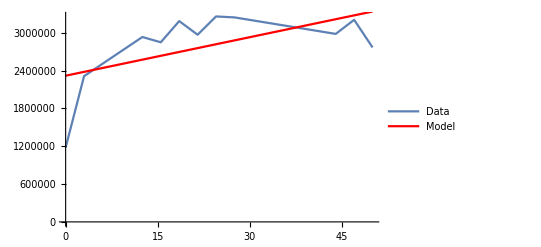

MAE: 378326.

R:0.325236

```mathematica
{Rest@dataᵀ⟦3⟧,Rest@dataᵀ⟦4⟧}ᵀ
LinearModelFit[%,x,x]
Show[ListLinePlot[%%,PlotLegends->{"Data"}],Plot[%[x],{x,0,50},PlotStyle->Red,PlotLegends->{"Model"}]]
Table[%%[x],{x,Rest@dataᵀ⟦3⟧}];
StringForm["MAE: ``",Mean@Abs[Rest@dataᵀ⟦4⟧-%]]
StringForm["R:``",CoefficientRR[ Rest@dataᵀ⟦4⟧, %%]]
```

{{0.,1.17092×10^6},{3.,2.41034×10^6},{12.5,1.67332×10^6},{15.5,1.3036×10^6},{18.5,1.05462×10^6},{21.5,745948.},{24.5,668983.},{27.5,531915.},{44.,145377.},{47.,89010.8},{50.,52343.9}}

FittedModel[1.79817×10^6-37627. x]

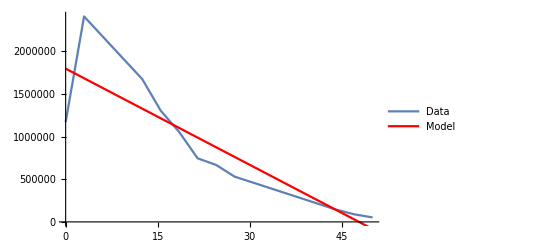

MAE: 246692.

R:0.768515

```mathematica
{Rest@dataᵀ⟦3⟧,Rest@dataᵀ⟦20⟧}ᵀ
LinearModelFit[%,x,x]
Show[ListLinePlot[%%,PlotLegends->{"Data"}],Plot[%[x],{x,0,50},PlotStyle->Red,PlotLegends->{"Model"}]]
Table[%%[x],{x,Rest@dataᵀ⟦3⟧}];
StringForm["MAE: ``",Mean@Abs[Rest@dataᵀ⟦20⟧-%]]
StringForm["R:``",CoefficientRR[ Rest@dataᵀ⟦20⟧, %%]]
```

### Calculating dynamics of data

```mathematica
slope[lin_]:= ArcTan[D[Normal[lin],x]]
```

Data dynamics: 1.52245×10^6

FittedModel[2.2078×10^6+20065.3 x]

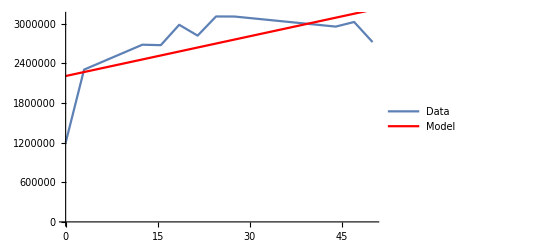

Angle of inclination: 1.57075

```mathematica
StringForm["Data dynamics: ``",(Last@# - First@#)& @Rest@dataᵀ⟦5⟧](*разность между первым измерением и последним*)
{Rest@dataᵀ⟦3⟧,Rest@dataᵀ⟦5⟧}ᵀ;
LinearModelFit[%,x,x]
Show[ListLinePlot[%%,PlotLegends->{"Data"}],Plot[%[x],{x,0,50},PlotStyle->Red,PlotLegends->{"Model"}]]
StringForm["Angle of inclination: ``",slope[%%]](*угол наклона*)
```

Data dynamics: 2.88953×10^6

FittedModel[2.52766×10^6+44962. x]

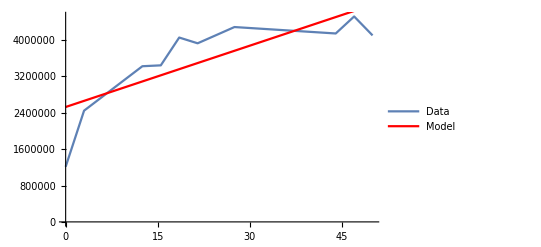

Angle of inclination: 1.57077

```mathematica
StringForm["Data dynamics: ``",(Last@# - First@#)& @Rest@dataᵀ⟦9⟧] (*разность между первым измерением и последним*)
{Rest@dataᵀ⟦3⟧,Rest@dataᵀ⟦9⟧}ᵀ;
LinearModelFit[%,x,x]
Show[ListLinePlot[%%,PlotLegends->{"Data"}],Plot[%[x],{x,0,50},PlotStyle->Red,PlotLegends->{"Model"}]]
StringForm["Angle of inclination: ``",slope[%%]](*угол наклона*)
```